```mathematica
F[x1_,x2_,x3_,x4_]=(1-(1-x1)*(1-x2))*(1-(1-x2)*(1-x3))*(1-(1-x3)*(1-x4));
φ[x1_,x2_,x3_,x4_]=Expand[F[x1,x2,x3,x4]]/.{x1^n_->x1,x2^n_->x2, x3^n_->x3,x4^n_->x4};
R[t_]=φ[Exp[-t],Exp[-t],Exp[-t],Exp[-t]]
λ[t_]=D[-Log[R[t]],t];
f[t_]=-D[R[t],t];
```

-2 ⅇ^(-3 t)+3 ⅇ^(-2 t)

0.833333

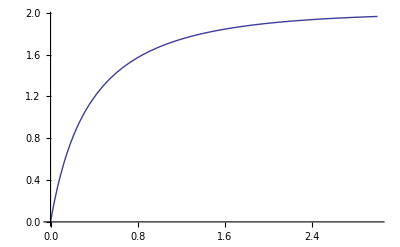

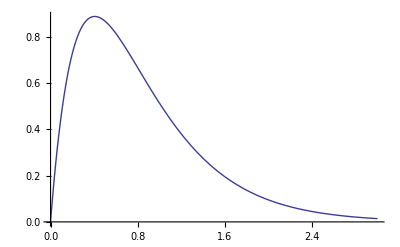

```mathematica
N[Integrate[R[t],{t,0,Infinity}]]
Plot[λ[t],{t,0,3}]
dens=Plot[f[t],{t,0,3}]
```

0.828715

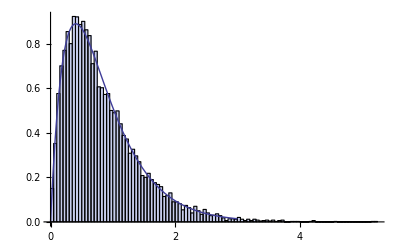

```mathematica
Needs["Histograms`"]
n=4;
k=2;
m=10000;
h=0;
θ=1;
TS=Table[0,{m}];
Do[
T=RandomReal[ExponentialDistribution[θ],n];
t1=Max[T[[1]],T[[2]]];
t2=Max[T[[2]],T[[3]]];
t3=Max[T[[3]],T[[4]]];
TS[[a]]=Min[t1,t2,t3];
,{a,1,m}];
meanTS=N[Sum[TS[[a]],{a,1,m}]/m]
hp1=Histogram[TS,HistogramScale->1];
Show[hp1,dens]
```